## Interpret the SBM results for new hypergraph diffusion.

### Plotting and utility functions

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<MaTeX`
```

```mathematica
ratioLatex=MaTeX["q/p", FontSize->16]
```

-Graphics-

```mathematica
diffusionLatex=MaTeX["\\textsc{FBC}", FontSize->15]
```

-Graphics-

```mathematica
approxDiffusionLatex=MaTeX["\\textsc{FBCA}", FontSize->15]
```

-Graphics-

```mathematica
cliqueLatex=MaTeX["\\textsc{CC}", FontSize->15]
```

-Graphics-

```mathematica
showResults[res_]:=With[{
hypBipartitenesses=results[All,{"clique_hyp_bipart","approx_diff_hyp_bipart"}],
cliqueBipartitenesses=results[All,{"clique_clique_bipart","approx_diff_clique_bipart"}],
times=results[All,{"clique_runtime","approx_diff_runtime"}]
},
Grid[{
{ListLinePlot[Transpose[hypBipartitenesses]]},
{ListLinePlot[Transpose[cliqueBipartitenesses],PlotRange->Automatic]},
{ListLinePlot[Transpose[times]]},
{ListLinePlot[times[All,(#"approx_diff_runtime"/#"clique_runtime")&]]}
}]
]
```

Define a nice plotting function.

```mathematica
nicePlot[curves_,style_,axes_,legend_,legendLoc_,plotRange_]:=
ListLinePlot[curves,
ScalingFunctions->{"Linear","Linear"},
PlotRange->plotRange,
PlotStyle->((Directive[Thickness[0.008],#[[1]],#[[2]]])&/@style),
LabelStyle->Directive[Bold,Medium,Black],
Frame->{True,True,False,False},
FrameStyle->Directive[Thick],
FrameTicksStyle->Directive[Thick],
FrameLabel->axes,
Epilog->Inset[
Framed[LineLegend[(Directive[Thickness[0.008],#[[1]],#[[2]]])&/@style,legend,LabelStyle->Directive[Bold,Medium,Black]]],
legendLoc,
Background->White]
]
```

```mathematica
nicePlot[curves_,colors_,axes_,legend_,legendLoc_]:=nicePlot[curves,colors,axes,legend,legendLoc,Automatic]
```

```mathematica
getExact[curve_]:=({#[[1]],If[Head[#[[2]]]===Around,#[[2]][[1]],#[[2]]]})&/@curve
```

```mathematica
nicePlotError[curves_,style_,axes_,legend_,legendLoc_,plotRange_]:=
With[
{p1=ListPlot[curves,
ScalingFunctions->{"Linear","Linear"},
PlotRange->plotRange,
PlotMarkers->{""},
PlotStyle->((#[[1]])&/@style),
LabelStyle->Directive[Bold,Medium,Black],
Frame->{True,True,False,False},
FrameStyle->Directive[Thick],
FrameTicksStyle->Directive[Thick],
FrameLabel->axes,
Epilog->Inset[
Framed[LineLegend[(Directive[Thickness[0.008],#[[1]],#[[2]]])&/@style,legend,LabelStyle->Directive[Bold,Medium,Black]]],
legendLoc,
Background->White]
],
p2=ListLinePlot[Map[getExact,curves],
ScalingFunctions->{"Linear","Linear"},
PlotRange->plotRange,
PlotStyle->((Directive[Thickness[0.008],#[[1]],#[[2]]])&/@style),
LabelStyle->Directive[Bold,Medium,Black],
Frame->{True,True,False,False},
FrameStyle->Directive[Thick],
FrameTicksStyle->Directive[Thick],
FrameLabel->axes,
Epilog->Inset[
Framed[LineLegend[(Directive[Thickness[0.008],#[[1]],#[[2]]])&/@style,legend,LabelStyle->Directive[Bold,Medium,Black]]],
legendLoc,
Background->White]
]},
Show[p1,p2]
]
```

```mathematica
selectFunc[r_]=(#ratio==r)&;
```

```mathematica
getRatioRange[res_,objective_,ratios_]:=({#,MeanAround[Normal[res[Select[selectFunc[#]],objective]]]})&/@ratios
```

### n=100, 3-Uniform, p=0.0001

```mathematica
results =SemanticImport["paper_results/two_cluster_average_results_100_3_0.0001_10.csv"][Select[#ratio≥2&&Mod[#ratio,0.5]==0&]];
```

```mathematica
allResults=SemanticImport["paper_results/two_cluster_results_100_3_0.0001.csv"][Select[#ratio≥2&&Mod[#ratio,0.5]==0&]];
```

```mathematica
hypBipartitenesses=results[All,{"clique_hyp_bipart","diff_hyp_bipart","approx_diff_hyp_bipart"}];
```

```mathematica
cliqueBipartitenesses=results[All,{"clique_clique_bipart","diff_clique_bipart","approx_diff_clique_bipart"}];
```

```mathematica
times=results[All,{"clique_runtime","diff_runtime","approx_diff_runtime"}];
```

```mathematica
shortTimes=results[All,{"clique_runtime","approx_diff_runtime"}];
```

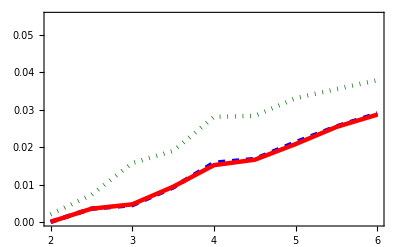

```mathematica
nicePlot[{
results[All,{"ratio","diff_hyp_bipart"}]//Values,
results[All,{"ratio","approx_diff_hyp_bipart"}]//Values,
results[All,{"ratio","clique_hyp_bipart"}]//Values
},
{{Blue,Dashed},{Red,Line},{Green//Darker//Darker,Dotted}},
{ratioLatex},
{"DiffusionLP","DiffusionApprox","CliqueCut"},
{30,0.041},
{{2,Automatic},{0,0.055}}]
```

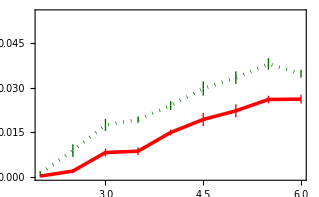

```mathematica
nicePlotError[{
getRatioRange[allResults,"diff_hyp_bipart",Range[2,6,0.5]],
getRatioRange[allResults,"approx_diff_hyp_bipart",Range[2,6,0.5]],
getRatioRange[allResults,"clique_hyp_bipart",Range[2,6,0.5]]
},
{{Blue,Dashed},{Red,Line},{Green//Darker//Darker,Dotted}},
{ratioLatex},
{"DiffusionLP","DiffusionApprox","CliqueCut"},
{30,0.041},
{{2,Automatic},{0,0.055}}
]
```

```mathematica
nicePlot[{
results[Select[#ratio≥2&],{"ratio","diff_clique_bipart"}]//Values,
results[Select[#ratio≥2&],{"ratio","approx_diff_clique_bipart"}]//Values,
results[Select[#ratio≥2&],{"ratio","clique_clique_bipart"}]//Values
},
{{Blue,Dashed},{Red,Line},{Green//Darker//Darker,Dotted}},
{ratioLatex},
{"Diffusion","Approx. Diffusion","Clique"},
{3.5,0.2},
{{2,Automatic},Automatic}];
```

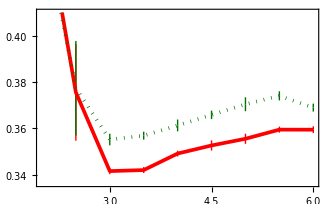

```mathematica
nicePlotError[{
getRatioRange[allResults,"diff_clique_bipart",Range[2,6,0.5]],
getRatioRange[allResults,"approx_diff_clique_bipart",Range[2,6,0.5]],
getRatioRange[allResults,"clique_clique_bipart",Range[2,6,0.5]]
},
{{Blue,Dashed},{Red,Line},{Green//Darker//Darker,Dotted}},
{ratioLatex},
{"Diffusion","Approx. Diffusion","Clique"},
{3.5,0.2},
{{2,Automatic},Automatic}]
```

```mathematica
nicePlot[{
results[All,{"ratio","diff_runtime"}]//Values,
results[All,{"ratio","approx_diff_runtime"}]//Values,
results[All,{"ratio","clique_runtime"}]//Values
},
{{Blue,Dashed},{Red,Line},{Green//Darker/Darker,Dotted}},
{ratioLatex},
{diffusionLatex,approxDiffusionLatex,cliqueLatex},
{4.75,12},
{{Automatic,Automatic},Automatic}];
```

```mathematica
nicePlotError[{
getRatioRange[allResults,"diff_runtime",Range[2,6,0.5]],
getRatioRange[allResults,"approx_diff_runtime",Range[2,6,0.5]],
getRatioRange[allResults,"clique_runtime",Range[2,6,0.5]]
},
{{Blue,Dashed},{Red,Line},{Green//Darker//Darker,Dotted}},
{ratioLatex},
{diffusionLatex,approxDiffusionLatex,cliqueLatex},
{5,12},
{{Automatic,Automatic},Automatic}]
```

-Graphics-

### n=1000, 5-uniform, p=10^-11

```mathematica
results =SemanticImport["paper_results/two_cluster_average_results_1000_5_1e-11_10.csv"][Select[#ratio>1&&Mod[#ratio,0.5]==0&]];
```

```mathematica
allResults=SemanticImport["paper_results/two_cluster_results_1000_5_1e-11.csv"][Select[#ratio>1&&Mod[#ratio,0.5]==0&]];
```

```mathematica
nicePlot[{
results[All,{"ratio","approx_diff_hyp_bipart"}]//Values,
results[All,{"ratio","clique_hyp_bipart"}]//Values
},
{{Red,Line},{Green//Darker//Darker,Dotted}},
{ratioLatex},
{approxDiffusionLatex,cliqueLatex},
{50,0.0083},
{{15,Automatic},{0,Automatic}}]
```

-Graphics-

```mathematica
nicePlotError[{
getRatioRange[allResults,"approx_diff_hyp_bipart",Range[2,30,0.5]],
getRatioRange[allResults,"clique_hyp_bipart",Range[2,30,0.5]]
},
{{Red,Line},{Green//Darker//Darker,Dotted}},
{ratioLatex},
{approxDiffusionLatex,cliqueLatex},
{50,0.0083},
{{15,Automatic},{0,Automatic}}];
```

```mathematica
nicePlot[{
results[All,{"ratio","approx_diff_clique_bipart"}]//Values,
results[All,{"ratio","clique_clique_bipart"}]//Values
},
{{Red,Line},{Green//Darker//Darker,Dotted}},
{ratioLatex},
{approxDiffusionLatex,cliqueLatex},
{126,0.445},
{{15,Automatic},Automatic}]
```

-Graphics-

```mathematica
nicePlotError[{
getRatioRange[allResults,"approx_diff_clique_bipart",Range[2,30,0.5]],
getRatioRange[allResults,"clique_clique_bipart",Range[2,30,0.5]]
},
{{Red,Line},{Green//Darker//Darker,Dotted}},
{ratioLatex},
{approxDiffusionLatex,cliqueLatex},
{22,0.445},
{{15,Automatic},Automatic}];
```

```mathematica
nicePlot[{
results[All,{"ratio","approx_diff_runtime"}]//Values,
results[All,{"ratio","clique_runtime"}]//Values
},
{{Red,Line},{Green//Darker//Darker,Dotted}},
{ratioLatex},
{diffusionLatex,approxDiffusionLatex,cliqueLatex},
{400,12},
{{Automatic,Automatic},Automatic}];
```

Show the F1-scores.

```mathematica
nicePlot[{
results[All,{"ratio","approx_diff_f1"}]//Values,
results[All,{"ratio","clique_f1"}]//Values
},
{{Red,Line},{Green//Darker//Darker,Dotted}},
{ratioLatex},
{approxDiffusionLatex,cliqueLatex},
{27,0.65},
{{15,Automatic},{Automatic,Automatic}}]
```

-Graphics-